```mathematica
Needs["FindBounce`"]
Quiet[Needs["VariationalMethods`"]];
(*RegisterExternalEvaluator["Python","/home/lugima/env/bin/python3"];*)
session=StartExternalSession["Python"];
```

## Functional derivatives implementation

(Source: Juan Carlo’s notebook :))

FunctionalD[L, ϕ, x, n, {δϕ1, δϕ2,...}]

Computes the nth functional derivative of an action
         
where  (the Lagrangian) is a local functional of . In general, the th functional derivative is a multi-linear differential operator that acts on test functions δϕ_1, ..., δϕ_n as:
         
where  is again some local functional. One of the test functions  always factorizes without derivatives, if one uses integration by parts.

The output of FunctionalD is the local functional . Its arguments are:
        - The Lagrangian L.
        - The field ϕ.
        - The integration variable x.
        - A list of  test functions δϕ1, δϕ2, ...

### Implementation

Since Mathematica can already do first functional derivatives with VariationalMethods`VariationalD, the only missing ingredient to implement higher functional derivatives is the observation that
        
So the function can be built recursively:

```mathematica
FunctionalD[L_, ϕ_, x_, 1] := VariationalD[L, ϕ[x], x];
FunctionalD[L_, ϕ_, x_, 1, {}] := FunctionalD[L, ϕ, x, 1];
FunctionalD[L_, ϕ_, x_, n_, {rest___, δϕLast_}] :=
If[n==Length[{rest, δϕLast}], 
δϕLast[x] FunctionalD[L, ϕ, x, n, {rest}], 
VariationalD[δϕLast[x] FunctionalD[L, ϕ, x, n - 1, {rest}], ϕ[x], x]];
```

### Perturbative expansion of action at its extremal (bounce)

(Source: Javi and Luis)

We expand the evaluation of the variation of a generic action S at its extremal

We do this perturbatively:

```mathematica
FunctionalSeries[F_,ϕ_,x_,n_]:=Sum[1/(k!)FuncD[F,ϕ,x,k,Table[δϕ,{j,1,k}]],{k,0,n}]
```

```mathematica
FunctionalSeriesCoeffs[F_,ϕ_,x_,n_]:=Table[1/(k!)FuncD[F,ϕ,x,k,Table[δϕ,{j,1,k}]],{k,0,n}]
```

```mathematica
(*Linearity in functionals*)
FuncD[F_+H_,ϕ_,x_,i_,δϕ_List]:=FuncD[F,ϕ,x,i,δϕ]+FuncD[H,ϕ,x,i,δϕ]
FuncD[ϵ F_,ϕ_,x_,i_,δϕ_List]:=ϵ FuncD[F,ϕ,x,i,δϕ]
FuncD[Power[ϵ,n_]F_,ϕ_,x_,i_,δϕ_List]:=Power[ϵ,n]FuncD[F,ϕ,x,i,δϕ]
(*Linearity in test functions*)
FuncD[F_,ϕ_,x_,i_,{δϕi___, δϕ1_ +δϕ2_ ,δϕf___}]:=FuncD[F,ϕ,x,i,{δϕi,δϕ1,δϕf}]+FuncD[F,ϕ,x,i,{δϕi,δϕ2,δϕf}]
FuncD[F_,ϕ_,x_,i_,{δϕi___, ϵ δϕ1_ ,δϕf___}]:=ϵ FuncD[F,ϕ,x,i,{δϕi,δϕ1,δϕf}]
FuncD[F_,ϕ_,x_,i_,{δϕi___, Power[ϵ,n_] δϕ1_ ,δϕf___}]:=Power[ϵ,n] FuncD[F,ϕ,x,i,{δϕi,δϕ1,δϕf}]
(*Recursion relation for higher order func. derivs.*)
FuncD[F_,ϕ_,x_,0,{}]:=F
FuncD[FuncD[F_,ϕ_,x_,i_,{δϕ1___}],ϕ_,x_,j_,{δϕ2___}]:=FuncD[F,ϕ,x,i+j,{δϕ1,δϕ2}]
```

```mathematica
(*Add as many terms as needed below to expand in powers of the perturbative parameter ϵ:*)
phiEoMs=CoefficientList[Normal[Series[FunctionalSeries[F0+ϵ F1+ϵ^2 F2,ϕ,x,2]/.δϕ->ϵ ϕ1+ϵ^2 ϕ2,{ϵ,0,2}]],ϵ]
```

Note: The prime derivatives denote functional derivatives (integrated in as many dummy variables as the number of derivatives, and times the fields they are multiplied by, evaluated at the same dummy variables).

## Modules

#### Module 0: LoadOperators

```mathematica
LoadOperators[η_]:=Module[
{},

Clear[m2,λ,κ,g,T, ϵ];

maxOrder=8;

(*η=1 for effective operators and η=0. for NO effective operators*)

(* Wilson coefficients and operators (BEFORE FIELD REDEFINITIONS) *)
(* After matching to the 4D theory at T>0,we find the following Wilson coefficients and operators in the 3dEFT Lagrangian: *)
(*O4*)
D2S2[r_]:=1/2 ϕ'[r]^2;
S2[r_]:=1/2 ϕ[r]^2;
S3[r_]:=ϕ[r]^3;
S4[r_]:=ϕ[r]^4;
opListO4={D2S2,S2,S3,S4};

K=1+g^2/(12 Pi^2);
m32pre=m2+g^2 T^2/6;
κ3pre=Sqrt[T] κ;
λ3pre=T λ;
coeffListO4={K,m32pre,κ3pre,λ3pre};

(*O6*)
S6[r_]:=ϕ[r]^6;
D4S2[r_]:=(2 ϕ'[r]+r ϕ''[r])^2/r^2;
D2S4[r_]:=ϕ[r]^3 (2 ϕ'[r]+r ϕ''[r])/r;
opListO6=η*{S6,D4S2,D2S4}; (*Sign from change to Euclidean is included in coefficients*)

c61pre=-(7*g^6*Zeta[3])/(192*Pi^4);
r61pre=-(7*g^2*Zeta[3])/(384*Pi^4*T^2);
r62pre=(35*g^4*Zeta[3])/(576*Pi^4*T);
coeffListO6=η*{c61pre,ϵ^4 r61pre,ϵ^2 r62pre};

(*O8*)
S8[r_]:=ϕ[r]^8;
D4S4A[r_]:=ϕ[r]^2 (2 ϕ'[r]^2/r^2+ϕ''[r]^2);
D6S2[r_]:=(2 ϕ'[r]+r ϕ''[r]) (4 ϕ'''[r]+r ϕ''''[r])/r^2;
D4S4B[r_]:=ϕ[r]^3 (4 ϕ'''[r]+r ϕ''''[r])/r;
D4S4C[r_]:=-3 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])^2/r^2;
D2S6[r_]:=ϕ[r]^5 (2 ϕ'[r]+r ϕ''[r])/r;
opListO8=η*{S8,D4S4A,D6S2,D4S4B,D4S4C,D2S6};(*Sign from change to Euclidean is included in coefficients*)

c81pre=(31*g^8*Zeta[5])/(2048*Pi^6*T);
c82pre=-(31*g^4*Zeta[5])/(10240*Pi^6*T^3);
r81pre=-(31*g^2*Zeta[5])/(10240*Pi^6*T^4);
r82pre=(217*g^4*Zeta[5])/(20480*Pi^6*T^3);
r83pre=(279*g^4*Zeta[5])/(20480*Pi^6*T^3);
r84pre=-(217*g^6*Zeta[5])/(5120*Pi^6*T^2);
coeffListO8=η*{c81pre,ϵ^4 c82pre,ϵ^6 r81pre,ϵ^4 r82pre,ϵ^4 r83pre,ϵ^2 r84pre};

(* In order to normalize canonically,we divide each coefficient by a power of K^(1/2) equal to the number of ϕ’s and expand up to order 8 in g.In doing this,the coefficients that go with each operator will gain different orders of g,so the same operators will appear in different perturbative orders with different coefficients. *)
powerCounting={g->ϵ g,m2->ϵ^2 m2, κ->ϵ^2 κ, λ->ϵ^2 λ}; (* Actually m2/T^2 ~ g^2 ~ κ/T *)

coeffListpre=Flatten[{coeffListO4,coeffListO6,coeffListO8}]/.powerCounting;
opList=Table[Flatten[{opListO4,opListO6,opListO8}][[i]]@r,{i,Length[Flatten[{opListO4,opListO6,opListO8}]]}];
nFields=Exponent[Collect[opList/.{ϕ->(n ϕ[#]&)},n],n];
coeffList = {1,m2, κ, λ, α61, β61, β62, α81, α82, β81, β82, β83, β84};
coeffListNorm=Normal[Series[#,{g,0,maxOrder}]]&/@(Power[K^(-1/2)/.powerCounting,#1]#2&[nFields,coeffListpre]);
coeffListNormMod=coeffListNorm/.Power[ϵ,m_/;m>maxOrder]->0;
LagList=CoefficientList[coeffListNorm.opList/.{Power[ϵ,m_]->If[m>maxOrder,0,Power[ϵ,m]]}//Expand,ϵ^2];
Lag0=Sum[LagList[[i]],{i,1,3}];
LagEFT=Table[LagList[[i]],{i,4,Length[LagList]}];

LagList=Flatten[{Lag0,LagEFT}];

PotList=(#/.Derivative[n_][ϕ_][r_]->0)&/@LagList;

(* Define the first order potential: *)
V0[ψ_]:=PotList[[1]]/.ϕ[r]->ψ;
coeffV0=DeleteCases[CoefficientList[V0[ϕ],ϕ],0];

];
```

#### Module 1: LoadV0andPhi6

```mathematica
LoadV0andPhi6[]:=Module[
{},

D2S2[r_]:=1/2 ϕ'[r]^2;
S2[r_]:=1/2 ϕ[r]^2;
S3[r_]:=ϕ[r]^3;
S4[r_]:=ϕ[r]^4;
opListO4={D2S2,S2,S3,S4};

K=1;
m32pre=m2+g^2 T^2/6;
κ3pre=Sqrt[T] κ;
λ3pre=T λ;
coeffListO4={K,m32pre,κ3pre,λ3pre};

(*O6*)
S6[r_]:=ϕ[r]^6;
opListO6={S6}; (*Sign from change to Euclidean is included in coefficients*)

c61pre=-(7*g^6*Zeta[3])/(192*Pi^4);
coeffListO6=η*{c61pre};

coeffList=Flatten[{coeffListO4,coeffListO6}];
opList=Table[Flatten[{opListO4,opListO6}][[i]]@r,{i,Length[Flatten[{opListO4,opListO6}]]}];

LagList=CoefficientList[coeffList.opList//Expand, η];

PotList=(#/.Derivative[n_][ϕ_][r_]->0)&/@LagList;

(* Define the first order potential: *)
V0[ψ_]:=PotList[[1]]/.ϕ[r]->ψ;
coeffV0=DeleteCases[CoefficientList[V0[ϕ],ϕ],0];

];
```

#### Module 2: EffOpsPotValues

```mathematica
EffOpsPotValues[line_]:=Module[{V0values, V1values, V2values,gTList, gList, TnucList, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders},

Clear[m2, κ, λ];
(* Load potential with eff. ops. *)
LoadOperators[1];
orderPerturb=2;

(* For the input model, get parameters and scan over g's and Tnuc's *)
m2 = line[[2]];
κ=line[[3]];
λ=line[[4]];

gTList=DeleteCases[{#[[1]],#[[2]]}&/@line[[5]],{x_,0}];
gList=#[[1]]&/@gTList;
TnucList=#[[2]]&/@gTList;

V0values={}; V1values={}; V2values={};
Do[
 Clear[g, T,ϕT0, ϕT1, ϵ];
{g, T}= {gList[[j]], TnucList[[j]]};

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Compute perturbative value of V at true vacuum order by order *)
EαOrders=CoefficientList[(Normal[Series[V[ϕTTotal],{ϵ,0,orderPerturb}]]/.solT), ϵ];

V0values=AppendTo[V0values,{g, EαOrders[[1]]}];
V1values=AppendTo[V1values,{g, EαOrders[[2]]}];
V2values=AppendTo[V2values,{g, EαOrders[[3]]}]; 

,{j, Length[gList]}];

Return[{V0values, V1values, V2values}]
]
```

#### Module 3: EffOpsPotValuesNew

```mathematica
EffOpsPotValuesNew[]:=Module[{V0val, V1val, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders},

(* Load potential with eff. ops. *)
LoadV0andPhi6[];
orderPerturb=2;

 Clear[ϕT0, ϕT1, ϵ];

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Compute perturbative value of V at true vacuum order by order *)
EαOrders=CoefficientList[(Normal[Series[V[ϕTTotal],{ϵ,0,orderPerturb}]]/.solT), ϵ];

V0val={α, EαOrders[[1]]};
V1val={α, EαOrders[[2]]};

Return[{V0val, V1val}]
]
```

#### Module 4:VEVShiftNew

```mathematica
VEVShiftNew[]:=Module[{V0values, V1values, V2values,gTList, gList, TnucList, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders},

(* Load potential with eff. ops. *)
LoadV0andPhi6[];
orderPerturb=2;

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Compute perturbative value of V at true vacuum order by order *)
δvev=Abs[(ϕTList[[1]]-ϕTTotal)/ϕTList[[1]]]/.solT/.ϵ->1;

Return[δvev]

]
```

#### Module 1: ComputeDerivs

```mathematica
ComputeDerivs:=ExternalEvaluate[session,
"import numpy as np

def compute_derivs(r, phi, numberDeriv):

	derivs = [phi]
	for i in range(1, numberDeriv+1):
		derivs.append(np.gradient(derivs[-1]) / np.gradient(r))

	return derivs[1:] # No returning phi

 "];
```

#### Module 2: FindBounce (CosmoTransitions)

```mathematica
FindBounce:=ExternalEvaluate[session,
"from cosmoTransitions.tunneling1D import SingleFieldInstanton
import numpy as np

def cosmo_transitions(V, phi_t, phi_f, numberDeriv, xtol=1e-4, phitol=1e-4, npoints=500):

	c2 = V[0]
	c3 = V[1]
	c4 = V[2]

	instanton = SingleFieldInstanton(
        phi_t,
        phi_f,
        lambda phi: c2 * phi ** 2 + c3 * phi ** 3 + c4 * phi ** 4,
        lambda phi: 2 * c2 * phi + 3 * c3 * phi ** 2 + 4 * c4 * phi ** 3,
        lambda phi: 2 * c2 + 6 * c3 * phi + 12 * c4 * phi ** 2,
        alpha=2, # Number of spacetime dimensions minus one
	)

	profile = instanton.findProfile(xtol=xtol, phitol=phitol, npoints=npoints)
	r, phi, dphi = profile.R, profile.Phi, profile.dPhi

	# Cannot use the previously defined function in this one because it is automatically translated to Mathematica
	derivs = [dphi]
	for i in range(2, numberDeriv+1):
		derivs.append(np.gradient(derivs[-1]) / np.gradient(r))

	return r, phi, derivs

 "];
```

#### Module 3: SolveBounce

```mathematica
SolveBounce[m20_,κ0_,λ0_,g0_,T0_,orderPerturb0_, PlotBounces_]:=
Module[
{ orderPerturb=orderPerturb0,
 minima,phiT,phiF,bf,bounce,ϕbounce0,L,V,phiBCs,phiEoMs,solBC,sol, action0},

{m2,κ,λ,g,T}={m20,κ0,λ0,g0,T0};

ϕList=Table[ToExpression["ϕ"<>ToString[i]],{i,0,orderPerturb-1}];
ϕmin:=Sum[ϵ^i ToExpression["ϕ"<>ToString[i]],{i,0,orderPerturb-1}];
ϕInfList=Table[Subscript[ToExpression["ϕ"<>ToString[i]], ∞],{i,0,orderPerturb-1}];
ϕminInf:=Sum[ϵ^i Subscript[ToExpression["ϕ"<>ToString[i]], ∞],{i,0,orderPerturb-1}];
Clear[ϕ0,ϕ1,ϕb];

(*** Compute EoMs ***)
L[r_]:=Sum[ϵ^(i-1) 4 Pi r^2 LagList[[i]],{i,1,Length[LagList]}];
V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];

phiEoMs:=CoefficientList[Normal[Series[FunctionalSeries[FuncD[L[r],ϕ,r,1,{}],ϕ,r,orderPerturb]/.δϕ->ϕmin-ϕ0,{ϵ,0,orderPerturb-1}]],ϵ]/.FuncD->FunctionalD/.{ϕ->ϕ0};
phiBCs := CoefficientList[Normal[Series[V'[ϕminInf],{ϵ,0,orderPerturb-1}]],ϵ];

numberDeriv = Max[Table[Exponent[phiEoMs[[i]]/.{Power[ϕ_,m_]->ϕ}/.{Derivative[n_][ϕ_][r_]->numD^n Derivative[n][ϕ][r]}, numD], {i, Length[phiEoMs]}]];

(*** Compute zeroth order bounce ***)
minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];
phiF=Select[minima, V0[#]==Max[Map[V0, minima]]&][[1]];

coefs=DeleteCases[N@CoefficientList[V0[ϕ],ϕ],0.];

Clear[radii,bounce0,bounce0Derivs];
{radii,bounce0,bounce0Derivs}=FindBounce[coefs, phiT, phiF, numberDeriv, N[10^-6], N[10^-6],1000];

fieldSust={ϕ0[r_]->Interpolation[Table[{radii[[j]],bounce0[[j]]},{j,1,Length[radii]}]][r]};

derivsSust=Table[
Derivative[k][ϕ0][r_]->Interpolation[
Table[{radii[[j]],bounce0Derivs[[k]][[j]]},{j,1,Length[radii],9}]
][r],{k,1,numberDeriv}];

(*** Compute bounce corrections ***)
solBC={Subscript[ϕ0, ∞]->phiF};
Do[
Clear[sust];
solBC=
Flatten[
AppendTo[solBC, Solve[(phiBCs[[i]]/.solBC)==0, ϕInfList[[i]]]]];
(*Obtain ϕk substitution as solution to kth EoM*)
sust=NDSolve[{(phiEoMs[[i]]/.fieldSust/.derivsSust)==0,ϕList[[i]][Last[radii]]==ϕInfList[[i]]/.solBC,  ϕList[[i]]'[radii[[2]]]==0}, 
 ϕList[[i]], {r,radii[[2]],Last[radii]},MaxSteps->10^8 ,Method->"StiffnessSwitching"]//Flatten;
(*Append ϕk substitution to list of ϕ(<k) substitutions*)
fieldSust=Flatten[AppendTo[fieldSust,ϕList[[i]][r_]->(ϕList[[i]]/.sust)@r]];
(*Convert ϕk solution to numerical values and compute its numerical derivatives*)
ϕnewDerivs=ComputeDerivs[radii[[2;;]], Table[(ϕList[[i]]/.sust)@radii[[j]], {j,2, Length[radii]}], numberDeriv];
(*Append d^n ϕk/dr^n substitutions to list of d^n ϕ(<k)/dr^n substitutions*)

derivsSust=Flatten[
AppendTo[derivsSust,
Table[
Derivative[k][ϕList[[i]]][r_]->Interpolation[
Table[{radii[[j]],ϕnewDerivs[[k]][[j]]},{j,2,Length[ϕnewDerivs[[k]]],10}]][r],{k,1,numberDeriv}]]],

{i,2,orderPerturb}];

(*Plot bounce solution up to 1st correction*)
If[PlotBounces==True, 
ϕ0plot[r_]=ϕ0[r]/.fieldSust;
ϕ1plot[r_]=ϕ1[r]/.fieldSust;
ϕbplot[r_]=ϕ0plot[r]+ϕ1plot[r];

Print[Show[Plot[ϕ0plot[r],{r,radii[[2]],Last[radii]}],
Plot[ϕ1plot[r],{r,radii[[2]],Last[radii]}],
Plot[ϕbplot[r],{r,radii[[2]],Last[radii]}, PlotLabel->"Full bounce T="<>ToString[T]], ImageSize->300]];
Print[Plot[V0[y], {y, phiF, phiT}, PlotLabel->"Potential", ImageSize->300]];
];

Return[{{radii},{fieldSust},{derivsSust}}] (*Return substitution list for bounce at each order*)
]
```

#### Module 4: ComputeAction

```mathematica
ComputeAction[m20_,κ0_,λ0_,g0_,T0_,orderPerturb0_]:=
Module[
{ m2=m20,κ=κ0,λ=λ0,g=g0,T=T0,orderPerturb=orderPerturb0,
 ϕList, ϕmin, rFin, sol, L, actionInt, action, action0, radii, fieldSust, derivsSust},
Clear[ϕ0, ϕ1,ϵ];
ϕList=Table[ToExpression["ϕ"<>ToString[i]],{i,0,orderPerturb-1}];
ϕmin:=Sum[ϵ^i ToExpression["ϕ"<>ToString[i]],{i,0,orderPerturb-1}]; (*Esto en principio debería incluir el ϕ2 también, pero los términos en la acción desarrolladas perturb que van con él tienen que dar cero por las EoM*)

(*Compute full bounce solution*)
{{radii}, {fieldSust}, {derivsSust}}=SolveBounce[m2,κ,λ,g,T,orderPerturb, False];

(*** Compute action ***)
Clear[L];
L=Sum[ϵ^(i-1) 4 Pi r^2 LagList[[i]],{i,1,Length[LagList]}];

(*Perturbative action*)
actionInt=Normal[Series[FunctionalSeries[L,ϕ,r,orderPerturb]/.{δϕ->ϕmin-ϕ0},{ϵ,0,orderPerturb}]]/.{FuncD->FunctionalD}/.{ϕ->ϕ0}/.fieldSust/.derivsSust/.ϵ->1;
action=NIntegrate[actionInt, {r, radii[[2]], Last[radii]}, AccuracyGoal->0.01, MinRecursion->10, MaxRecursion->20]; (*Integrating up to rFin is equivalent to ∞ bc the bounce is constantly 0 beyond this radius*)

Return[action]
]
```

#### Module 5: EffOpsValuesBoop

```mathematica
EffOpsValuesBoop[line_]:=Module[{V0values, V1values, S0values,S1values,gTList, gList, TnucList, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders, ϕList, ϕmin, rFin, sol, L, actionInt, action, action0, radii, fieldSust, derivsSust},

Clear[m2, κ, λ];
(* Load potential with eff. ops. *)
LoadV0andPhi6[];
orderPerturb=2;

(* For the input model, get parameters and scan over g's and Tnuc's *)
m2 = line[[2]];
κ=line[[3]];
λ=line[[4]];

gTList=DeleteCases[{#[[1]],#[[2]]}&/@line[[5]],{x_,0}];
gList=#[[1]]&/@gTList;
TnucList=#[[2]]&/@gTList;

V0values={}; V1values={}; 
S0values={};S1values={}; 
Do[
 Clear[g, T,ϕT0, ϕT1, ϵ];
{g, T}= {gList[[j]], TnucList[[j]]};

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Compute perturbative value of V at true vacuum order by order *)
EαOrders=CoefficientList[(Normal[Series[V[ϕTTotal],{ϵ,0,orderPerturb}]]/.solT), ϵ];

V0values=AppendTo[V0values,{g, EαOrders[[1]]}];
V1values=AppendTo[V1values,{g, EαOrders[[2]]}];

(* Compute full bounce solution (almost copied from ComputeAction)*)
ϕmin:=Sum[ϵ^i ToExpression["ϕ"<>ToString[i]],{i,0,orderPerturb-1}]; 
{{radii}, {fieldSust}, {derivsSust}}=SolveBounce[m2,κ,λ,g,T,orderPerturb, False];

(*** Compute action ***)
Clear[L];
L=Sum[ϵ^(i-1) 4 Pi r^2 LagList[[i]],{i,1,Length[LagList]}];

(* Action *)
actionInts=CoefficientList[Normal[Series[FunctionalSeries[L,ϕ,r,orderPerturb]/.{δϕ->ϕmin-ϕ0},{ϵ,0,orderPerturb}]]/.{FuncD->FunctionalD}/.{ϕ->ϕ0}/.fieldSust/.derivsSust, ϵ];
(*Print[Normal[Series[FunctionalSeries[L,ϕ,r,orderPerturb]/.{δϕ->ϕmin-ϕ0},{ϵ,0,orderPerturb}]]/.{FuncD->FunctionalD}];*)
S0val=NIntegrate[actionInts[[1]], {r, radii[[2]], Last[radii]}, AccuracyGoal->0.01, MinRecursion->10, MaxRecursion->20];
S1val=NIntegrate[actionInts[[2]], {r, radii[[2]], Last[radii]}, AccuracyGoal->0.01, MinRecursion->10, MaxRecursion->20];

S0values=AppendTo[S0values,{g,S0val}];
S1values=AppendTo[S1values,{g, S1val}];

,{j, Length[gList]}];

Return[{V0values, V1values, S0values, S1values}]
]
```

#### Module 3: VEVShift

```mathematica
VEVShift[line_]:=Module[{V0values, V1values, V2values,gTList, gList, TnucList, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders},

Clear[m2, κ, λ];
(* Load potential with eff. ops. *)
LoadV0andPhi6[];
orderPerturb=2;

(* For the input model, get parameters and scan over g's and Tnuc's *)
m2 = line[[2]];
κ=line[[3]];
λ=line[[4]];

gTαList=DeleteCases[{#[[1]],#[[2]],#[[3]]}&/@line[[5]],{x_,0,0}];
gList=#[[1]]&/@gTαList;
TnucList=#[[2]]&/@gTαList;
αList=#[[3]]&/@gTαList;

δvevgList={};δvevαList={};
Do[
 Clear[g, T,α,ϕT0, ϕT1, ϵ];
{g, T,α}= {gList[[j]], TnucList[[j]],αList[[j]]};

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Compute perturbative value of V at true vacuum order by order *)
δvev=Abs[(ϕTList[[1]]-ϕTTotal)/ϕTList[[1]]]/.solT/.ϵ->1;
δvevgList = AppendTo[δvevgList, {g,δvev}];
δvevαList=AppendTo[δvevαList,{α,δvev}];

,{j, Length[gList]}];

Return[{δvevgList,δvevαList}]

]
```

#### Module 4: RunawayCondition

```mathematica
RunawayCondition[lineWO_]:=Module[{V0values, V1values, V2values,gTList, gList, TnucList, ϕTList, ϕTTotal, minima, phiT0, V, phiTEqs, solT, EαOrders},

Clear[m2, κ, λ];
(* Load potential with eff. ops. *)
LoadOperators[1, False];
orderPerturb=2;

(* For the input model, get parameters and scan over g's and Tnuc's *)
m2 = lineWO[[2]];
κ=lineWO[[3]];
λ=lineWO[[4]];

gTList=DeleteCases[{#[[1]],#[[2]]}&/@lineWO[[5]],{x_,0}];
gList=#[[1]]&/@gTList;
TnucList=#[[2]]&/@gTList;

α∞values={};
Do[
 Clear[g, T,ϕT0, ϕT1, ϵ];
{g, T}= {gList[[j]], TnucList[[j]]};

(* Find ϕT0 from V0 *)
ϕTList=Table[ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];
ϕTTotal:=Sum[ϵ^i ToExpression["ϕT"<>ToString[i]],{i,0,orderPerturb-1}];

minima = ϕ/.NSolve[D[V0[ϕ],ϕ]==0&&D[V0[ϕ],{ϕ,2}]>0,ϕ,Reals];
phiT0 = Select[minima, V0[#]==Min[Map[V0, minima]]&][[1]];

V[ψ_]:=Sum[ϵ^(i-1)PotList[[i]]/.{ϕ[r]->ψ},{i,1,Length[PotList]}];
phiTEqs := CoefficientList[Normal[Series[V'[ϕTTotal],{ϵ,0,orderPerturb-1}]],ϵ];

solT={ϕT0->phiT0};
Do[
solT=
Flatten[
AppendTo[solT, Solve[(phiTEqs[[i]]/.solT)==0, ϕTList[[i]]]]]
,
{i,2,orderPerturb}];

(* Not very well calculated perturbatively because we should also expand the quotient in perturbative orders of Tnuc, which we lack*)
vev=( ϕTTotal/.solT)/.ϵ->1;
a∞ = 4.9*10^(-3) vev^2/T; (* Definition changed for 3D case wrt 4.9*10^(-3) vev^2/T^2*)
α∞values=AppendTo[α∞values,{g,a∞}];

,{j, Length[gList]}];

Return[α∞values]
]
```

#### Module 5: Other functions

```mathematica
whereSPT[results_]:=Module[{newresults,linelist},
newresults={};
linelist={};
Do[
Do[
If[Max[#[[3]]&/@results[[line]][[gchnum]][[5]]]>0.08,
AppendTo[newresults,results[[line]][[gchnum]]];
AppendTo[linelist,{line,gchnum}];
]
,{gchnum,Length[results[[line]]]}
]
,{line,Length[results]}
];
Return[{{newresults},{linelist}}];
]

getParams[list_]:=Module[{Tn,α,β,V0,V1,V2,S0,S1,S2},
Tn=DeleteCases[{#[[1]],#[[2]]}&/@list,{x_,0}];
α=DeleteCases[{#[[1]],#[[3]]}&/@list,{x_,0}];
β=DeleteCases[{#[[1]],#[[4]]}&/@list,{x_,0}];
V0=DeleteCases[{#[[1]],#[[5]]}&/@list,{x_,0}];
V1=DeleteCases[{#[[1]],#[[6]]}&/@list,{x_,0}];
V2=DeleteCases[{#[[1]],#[[7]]}&/@list,{x_,0}];
(*S0=DeleteCases[{#[[1]],#[[8]]}&/@list,{x_,0}];
S1=DeleteCases[{#[[1]],#[[9]]}&/@list,{x_,0}];
S2=DeleteCases[{#[[1]],#[[10]]}&/@list,{x_,0}];
Return[{Tn,α,β,V0,V1,V2,S0,S1,S2}];*)
Return[{Tn,α,β,V0,V1,V2}]
]
```

## Scan

```mathematica
(* Load all models with GW parameters *)
Quiet@Get[NotebookDirectory[]<>"PT_results_preDR.txt"];
resultsPre = results;
Quiet@Get[NotebookDirectory[]<>"PT_results_WO.txt"];
resultsWO = results;
Quiet@Get[NotebookDirectory[]<>"PT_results_W.txt"];
resultsW = results;
```

```mathematica
(* Keep those models where there exists a g such that there is a SPT without eff. ops. *)
{newresults,linelist}=whereSPT[resultsW];
newresults[[1]][[21]]
```

{0.791454,57930.5,-114.706,0.0711575,{{0.05,0,0,0,0,0,0},{0.165994,0,0,0,0,0,0},{0.281988,0,0,0,0,0,0},{0.397981,959.65,0.000129216,654.026,-3.80566×10^6,-924.681,8.20763},{0.513975,710.718,0.000526296,470.294,-6.28646×10^6,-11762.9,244.363},{0.629969,554.773,0.00167161,353.276,-9.42659×10^6,-91147.4,3784.58},{0.745963,444.406,0.00484263,253.287,-1.36736×10^7,-531158.,36991.5},{0.861957,364.72,0.0130248,180.975,-1.88118×10^7,-2.45812×10^6,206594.},{0.977951,308.141,0.0340186,135.147,-2.41462×10^7,-9.16132×10^6,130169.},{1.04755,279.904,0.0675524,106.886,-2.78461×10^7,-1.90481×10^7,-2.48523×10^6},{1.05915,275.101,0.0775455,98.9404,-2.862×10^7,-2.15774×10^7,-3.6184×10^6},{1.07075,270.162,0.0899546,95.9863,-2.94752×10^7,-2.45028×10^7,-5.14773×10^6},{1.08234,264.942,0.105901,90.049,-3.04604×10^7,-2.79577×10^7,-7.2312×10^6},{1.09394,257.708,0.132299,79.263,-3.21073×10^7,-3.29022×10^7,-1.0468×10^7},{1.10554,249.691,0.170881,60.7169,-3.41164×10^7,-3.92585×10^7,-1.52963×10^7},{1.11714,240.827,0.229464,46.2886,-3.6562×10^7,-4.75839×10^7,-2.26873×10^7},{1.12874,0,0,0,0,0,0},{1.14034,0,0,0,0,0,0}}}

Max g

0.722609

-Graphics-

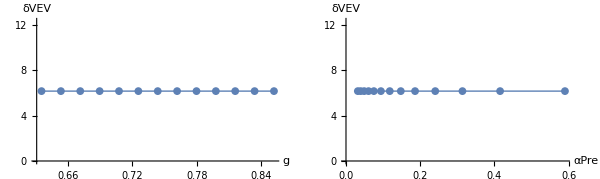

-Graphics-

-Graphics-

{{0.63514,0.0395529},{0.653228,0.0523072},{0.671315,0.0702993},{0.689403,0.0968805},{0.707491,0.138596},{0.725578,0.203736},{0.743666,0.307115},{0.761754,0.489696},{0.779841,0.791444},{0.797929,1.32631},{0.816017,2.26586},{0.834104,3.93273},{0.852192,7.01836},{0.87028,12.706},{0.888367,24.4571},{0.906455,48.8709},{0.917308,87.2072},{0.919116,96.6959},{0.920925,107.122},{0.922734,118.857},{0.924543,131.941},{0.926352,146.064},{0.92816,161.287},{0.929969,288.257}}

{{0.63514,0.0324633},{0.653228,0.040404},{0.671315,0.0502599},{0.689403,0.0624603},{0.707491,0.0774789},{0.725578,0.0970427},{0.743666,0.122418},{0.761754,0.154629},{0.779841,0.195289},{0.797929,0.254431},{0.816017,0.338667},{0.834104,0.465933},{0.852192,0.708787}}

```mathematica
(* Ejemplos en los que no se corta demasiado: 1, 6, 7, 8, 9  *)
(* En el ejemplo 12,14, hay una diferencia de factor casi 2 entre WO y W *)
{line,gchnum}=linelist[[1]][[1]];
{TnWO,αWO,βWO,V0WO,V1WO,V2WO}=getParams[resultsWO[[line]][[gchnum]][[5]]];
{TnW,αW,βW,V0W,V1W,V2W}=getParams[resultsW[[line]][[gchnum]][[5]]];
{TnPre,αPre,βPre,V0Pre,V1Pre,V2Pre}=getParams[resultsPre[[line]][[gchnum]][[5]]];

(* Shift in vev for simplified potential and ϕ6 correction *)
{δvevg, δvevα}=VEVShift[resultsPre[[line]][[gchnum]]];

(* Values for V0, V1, V2 computed using eff. ops. but for points obtained without eff. ops. *)
{V0addedW, V1addedW, V2addedW}=EffOpsPotValues[resultsWO[[line]][[gchnum]]];

(* Max α for which the EFT is still valid when including eff ops *)
aux1=Table[{Abs[V2W[[i]][[2]]/V1W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}];
aux2=Max[First/@aux1];
maxαPerturb=If[aux2>0.5,Interpolation[aux1][0.5], "Nope"];

Print["Max g"];
auxg1=Table[{Abs[V2W[[i]][[2]]/V1W[[i]][[2]]],αW[[i]][[1]]},{i,1,Length[αW]}];
auxg2=Max[First/@auxg1];
maxgPerturb=If[auxg2>0.5,Interpolation[auxg1][0.5], "Nope"]

(* Runaway condition *)
α∞ = RunawayCondition[resultsW[[line]][[gchnum]]];
fα=Interpolation[α∞, InterpolationOrder->1];
ming=Min[{TnW[[1]][[1]],TnWO[[1]][[1]], TnPre[[1]][[1]]} ];maxg=Max[{TnW[[-1]][[1]],TnWO[[-1]][[1]], TnPre[[-1]][[1]]} ]+0.01;

GraphicsRow[{
ListPlot[{TnPre,TnWO,TnW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"Pre DR","WO","W"},ImageSize->300,PlotStyle->{Thick,Dashed,Dotted},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"g","Tnuc"}]
,
Show[
Plot[fα[g],{g,ming,maxg},PlotLegends->{"Min α for runaway"},ImageSize->300, PlotStyle->Directive[AbsoluteThickness[2],Opacity[0.5],Black],PlotRange->{{ming,maxg},{0,All}},AxesOrigin->{Automatic, 0},Filling->{1->{Bottom,GrayLevel[.8]}}, FillingStyle->{Gray, Opacity[0.5]}]
,
ListPlot[{αPre,αWO,αW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"Pre DR","WO","W"},ImageSize->300,PlotStyle->{Thick,Dashed,Dotted},PlotRange->All, AxesLabel->{"g","α"}, AxesOrigin->{Automatic, 0}]
,
If[maxαPerturb!="Nope",Plot[maxαPerturb,{g,ming,maxg},PlotStyle->Red, PlotLegends->"Max. perturb. α", ImageSize->400],Plot[0,{g,ming,maxg},PlotStyle->Opacity[0], ImageSize->400] ]
 ]
,
ListPlot[{βPre,βWO,βW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"Pre DR","WO","W"},ImageSize->300,PlotStyle->{Thick,Dashed,Dotted},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"g","β/H"}, AxesOrigin->{Automatic, 0}]
},ImageSize->Full]

GraphicsRow[{
ListPlot[δvevg,Joined->True,PlotMarkers->{Automatic,8},ImageSize->300,PlotStyle->{Thick},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"g","δVEV"}]
,
ListPlot[δvevα,Joined->True,PlotMarkers->{Automatic,8},ImageSize->300,PlotStyle->{Thick},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"αPre","δVEV"}]
}, ImageSize->600]

GraphicsRow[{
ListPlot[{Table[{Abs[V1WO[[i]][[2]]/V0WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V1W[[i]][[2]]/V0W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","W"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V1/V0","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic],
ListPlot[{Table[{Abs[V2WO[[i]][[2]]/V1WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V2W[[i]][[2]]/V1W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","W"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V2/V1","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic]
}, ImageSize->Full]

GraphicsRow[{
ListPlot[{Table[{Abs[V1WO[[i]][[2]]/V0WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V1addedW[[i]][[2]]/V0addedW[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","Added W for WO points"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V1/V0","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic],
ListPlot[{Table[{Abs[V2WO[[i]][[2]]/V1WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V2addedW[[i]][[2]]/V1addedW[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","Added W for WO points"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V2/V1","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All,GridLines->Automatic]
}, ImageSize->Full]

αW
αWO
```

```mathematica
fα[maxgPerturb]
```

0.318797

```mathematica
Interpolation[αW][maxgPerturb]
Interpolation[αWO][maxgPerturb]
```

0.190815

0.0934667

```mathematica
Interpolation[βW][maxgPerturb]
Interpolation[βWO][maxgPerturb]
```

108.466

102.426

```mathematica
Interpolation[TnW][maxgPerturb]
Interpolation[TnWO][maxgPerturb]
```

788.128

763.503

```mathematica
(82.852-12.361)/82.852
```

0.850806

```mathematica
(* without pre dr, for those points where it couldn't compute shit *)
```

```mathematica
(* Ejemplos en los que no se corta demasiado: 1, 6, 7, 8, 9  *)
(* En el ejemplo 17,18,21 hay una diferencia de factor casi 2 entre WO y W *)
{line,gchnum}=linelist[[1]][[21]];
{TnWO,αWO,βWO,V0WO,V1WO,V2WO}=getParams[resultsWO[[line]][[gchnum]][[5]]];
{TnW,αW,βW,V0W,V1W,V2W}=getParams[resultsW[[line]][[gchnum]][[5]]];

(* Values for V0, V1, V2 computed using eff. ops. but for points obtained without eff. ops. *)
{V0addedW, V1addedW, V2addedW}=EffOpsPotValues[resultsWO[[line]][[gchnum]]];

(* Max α for which the EFT is still valid when including eff ops *)
aux1=Table[{Abs[V2W[[i]][[2]]/V1W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}];
aux2=Max[First/@aux1];
maxαPerturb=If[aux2>1,Interpolation[aux1][1], "Nope"];

(* Runaway condition *)
α∞ = RunawayCondition[resultsW[[line]][[gchnum]]];
fα=Interpolation[α∞, InterpolationOrder->1];
ming=Min[{TnW[[1]][[1]],TnWO[[1]][[1]]} ];maxg=Max[{TnW[[-1]][[1]],TnWO[[-1]][[1]]} ]+0.01;

GraphicsRow[{
ListPlot[{TnWO,TnW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"WO","W"},ImageSize->300,PlotStyle->{{Orange, Dashed},{Green,Dotted}},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"g","Tnuc"}]
,
Show[
Plot[fα[g],{g,ming,maxg},PlotLegends->{"Min α for runaway"},ImageSize->300, PlotStyle->Directive[AbsoluteThickness[2],Opacity[0.5],Black],PlotRange->{{ming,maxg},All},AxesOrigin->{Automatic, 0},Filling->{1->{Bottom,GrayLevel[.8]}}, FillingStyle->{Gray, Opacity[0.5]}]
,
ListPlot[{αWO,αW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"WO","W"},ImageSize->300,PlotStyle->{{Orange, Dashed},{Green,Dotted}},PlotRange->All, AxesLabel->{"g","α"}, AxesOrigin->{Automatic, 0}]
,
If[maxαPerturb!="Nope",Plot[maxαPerturb,{g,ming,maxg},PlotStyle->Red, PlotLegends->"Max. perturb. α", ImageSize->400],Plot[0,{g,ming,maxg},PlotStyle->Opacity[0], ImageSize->400] ]
 ]
,
ListPlot[{βWO,βW},Joined->True,PlotMarkers->{Automatic,8},PlotLegends->{"WO","W"},ImageSize->300,PlotStyle->{{Orange, Dashed},{Green,Dotted}},PlotRange->{{Automatic,Automatic},Automatic}, AxesLabel->{"g","β/H"}, AxesOrigin->{Automatic, 0}]
},ImageSize->Full]

GraphicsRow[{
ListPlot[{Table[{Abs[V1WO[[i]][[2]]/V0WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V1W[[i]][[2]]/V0W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","W"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V1/V0","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic],
ListPlot[{Table[{Abs[V2WO[[i]][[2]]/V1WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V2W[[i]][[2]]/V1W[[i]][[2]]],αW[[i]][[2]]},{i,1,Length[αW]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","W"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V2/V1","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic]
}, ImageSize->Full]

GraphicsRow[{
ListPlot[{Table[{Abs[V1WO[[i]][[2]]/V0WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V1addedW[[i]][[2]]/V0addedW[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","Added W for WO points"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V1/V0","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All, GridLines->Automatic],
ListPlot[{Table[{Abs[V2WO[[i]][[2]]/V1WO[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}],
Table[{Abs[V2addedW[[i]][[2]]/V1addedW[[i]][[2]]],αWO[[i]][[2]]},{i,1,Length[αWO]}]},PlotMarkers->{Automatic,8},ImageSize->400,PlotLegends->{"WO","Added W for WO points"},PlotStyle->ColorData[97,"ColorList"][[2;;]], AxesLabel->{"V2/V1","α"}, AxesOrigin->{Automatic, 0}, PlotRange->All,GridLines->Automatic]
}, ImageSize->Full]
αWO
αW
resultsW[[line]][[gchnum]]
```

-Graphics-

-Graphics-

-Graphics-

{{0.397981,0.000129216},{0.513975,0.000526623},{0.629969,0.00168026},{0.745963,0.00485871},{0.861957,0.0134538},{0.977951,0.0406891},{1.04755,0.0961328},{1.05915,0.124878}}

{{0.397981,0.000129216},{0.513975,0.000526296},{0.629969,0.00167161},{0.745963,0.00484263},{0.861957,0.0130248},{0.977951,0.0340186},{1.04755,0.0675524},{1.05915,0.0775455},{1.07075,0.0899546},{1.08234,0.105901},{1.09394,0.132299},{1.10554,0.170881},{1.11714,0.229464}}

{0.791454,57930.5,-114.706,0.0711575,{{0.05,0,0,0,0,0,0},{0.165994,0,0,0,0,0,0},{0.281988,0,0,0,0,0,0},{0.397981,959.65,0.000129216,654.026,-3.80566×10^6,-924.681,8.20763},{0.513975,710.718,0.000526296,470.294,-6.28646×10^6,-11762.9,244.363},{0.629969,554.773,0.00167161,353.276,-9.42659×10^6,-91147.4,3784.58},{0.745963,444.406,0.00484263,253.287,-1.36736×10^7,-531158.,36991.5},{0.861957,364.72,0.0130248,180.975,-1.88118×10^7,-2.45812×10^6,206594.},{0.977951,308.141,0.0340186,135.147,-2.41462×10^7,-9.16132×10^6,130169.},{1.04755,279.904,0.0675524,106.886,-2.78461×10^7,-1.90481×10^7,-2.48523×10^6},{1.05915,275.101,0.0775455,98.9404,-2.862×10^7,-2.15774×10^7,-3.6184×10^6},{1.07075,270.162,0.0899546,95.9863,-2.94752×10^7,-2.45028×10^7,-5.14773×10^6},{1.08234,264.942,0.105901,90.049,-3.04604×10^7,-2.79577×10^7,-7.2312×10^6},{1.09394,257.708,0.132299,79.263,-3.21073×10^7,-3.29022×10^7,-1.0468×10^7},{1.10554,249.691,0.170881,60.7169,-3.41164×10^7,-3.92585×10^7,-1.52963×10^7},{1.11714,240.827,0.229464,46.2886,-3.6562×10^7,-4.75839×10^7,-2.26873×10^7},{1.12874,0,0,0,0,0,0},{1.14034,0,0,0,0,0,0}}}

## Scatterplot of curves V1/V0 and S1/S0 vs α

```mathematica
(* -----------------------------------Lo que quiere Miki *)
```

```mathematica
(* Load all models with GW parameters *)
Quiet@Get[NotebookDirectory[]<>"PT_results_preDR_prueba2.txt"];
resultsPre = results;
Quiet@Get[NotebookDirectory[]<>"PT_results_WO_prueba2.txt"];
resultsWO = results;
Quiet@Get[NotebookDirectory[]<>"PT_results_W_prueba2.txt"];
resultsW = results;

(* Keep those models where there exists a g such that there is a SPT without eff. ops. *)
{newresults,linelist}=whereSPT[resultsPre];

listV1V0={};listS1S0={};
Do[
{line,gchnum}=linelist[[1]][[i]];
(*{TnWO,αWO,βWO,V0WO,V1WO,V2WO}=getParams[resultsWO[[line]][[gchnum]][[5]]];*)
{TnPre,αPre,βPre,Va0,Va1,Va2}=getParams[resultsPre[[line]][[gchnum]][[5]]];

{V0addedW, V1addedW, S0addedW, S1addedW}=EffOpsValuesBoop[resultsPre[[line]][[gchnum]]];

AppendTo[listV1V0,Table[{αPre[[k]][[2]],Abs[V1addedW[[k]][[2]]/V0addedW[[k]][[2]]]},{k,1,Length[αPre]}]];
AppendTo[listS1S0,Table[{αPre[[k]][[2]],Abs[S1addedW[[k]][[2]]/S0addedW[[k]][[2]]]},{k,1,Length[αPre]}]],

{i,1,Length[linelist[[1]]]}]
```

ExternalEvaluate::unknownSys: session is not a known system in the ExternalEvaluate Framework.

Set::shape: Lists {radii,bounce0,bounce0Derivs} and ExternalEvaluate[session,from cosmoTransitions.tunneling1D import SingleFieldInstanton
import numpy as np

def cosmo_transitions(V, phi_t, phi_f, numberDeriv, xtol=1e-4, phitol=1e-4, npoints=500):

	c2 = V[0]
	c3 = V[1]
	c4 = V[2]

	instanton = SingleFieldInstanton(
        phi_t,
        phi_f,
        lambda phi: c2 * phi ** 2 + c3 * phi ** 3 + c4 * phi ** 4,
        lambda phi: 2 * c2 * phi + 3 * c3 * phi ** 2 + 4 * c4 * phi ** 3,
        lambda phi: 2 * c2 + 6 * c3 * phi + 12 * c4 * phi ** 2,
        alpha=2, # Number of spacetime dimensions minus one
	)

	profile = instanton.findProfile(xtol=xtol, phitol=phitol, npoints=npoints)
	r, phi, dphi = profile.R, profile.Phi, profile.dPhi

	# Cannot use the previously defined function in this one because it is automatically translated to Mathematica
	derivs = [dphi]
	for i in range(2, numberDeriv+1):
		derivs.append(np.gradient(derivs[-1]) / np.gradient(r))

	return r, phi, derivs

 ][{66476.8,-2177.49,9.67647},145.099,0,0,1.×10^-6,1.×10^-6,1000] are not the same shape.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Last::normal: Nonatomic expression expected at position 1 in Last[radii].

Part::partd: Part specification radii⟦2⟧ is longer than depth of object.

Last::normal: Nonatomic expression expected at position 1 in Last[radii].

NDSolve::dvnoarg: The function ϕ0 appears with no arguments.

ReplaceAll::reps: {NDSolve[{-0.000371149 r^2 (Interpolation[{}][r])^6 FunctionalD^(1,0,0,0)[121.598 Power[«2»] Plus[«4»],ϕ0,r,1,{}] FunctionalSeries^(1,0,0,0)[VariationalD[Times[«3»],Interpolation[«1»][«1»],r],ϕ0,r,2]==0,ϕ1[Last[radii]]==0.,ϕ1'[radii⟦2⟧]==0},ϕ1,{r,radii⟦2⟧,Last[radii]},MaxSteps→100000000,Method→StiffnessSwitching]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ExternalEvaluate::unknownSys: session is not a known system in the ExternalEvaluate Framework.

Part::take: Cannot take positions 2 through -1 in radii.

Part::partd: Part specification radii⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[radii].

General::stop: Further output of Last::normal will be suppressed during this calculation.

NIntegrate::nlim: r = radii⟦2⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Set::shape: Lists {radii,bounce0,bounce0Derivs} and ExternalEvaluate[session,from cosmoTransitions.tunneling1D import SingleFieldInstanton
import numpy as np

def cosmo_transitions(V, phi_t, phi_f, numberDeriv, xtol=1e-4, phitol=1e-4, npoints=500):

	c2 = V[0]
	c3 = V[1]
	c4 = V[2]

	instanton = SingleFieldInstanton(
        phi_t,
        phi_f,
        lambda phi: c2 * phi ** 2 + c3 * phi ** 3 + c4 * phi ** 4,
        lambda phi: 2 * c2 * phi + 3 * c3 * phi ** 2 + 4 * c4 * phi ** 3,
        lambda phi: 2 * c2 + 6 * c3 * phi + 12 * c4 * phi ** 2,
        alpha=2, # Number of spacetime dimensions minus one
	)

	profile = instanton.findProfile(xtol=xtol, phitol=phitol, npoints=npoints)
	r, phi, dphi = profile.R, profile.Phi, profile.dPhi

	# Cannot use the previously defined function in this one because it is automatically translated to Mathematica
	derivs = [dphi]
	for i in range(2, numberDeriv+1):
		derivs.append(np.gradient(derivs[-1]) / np.gradient(r))

	return r, phi, derivs

 ][{65273.,-2126.3,9.22686},149.114,0,0,1.×10^-6,1.×10^-6,1000] are not the same shape.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

NDSolve::dvnoarg: The function ϕ0 appears with no arguments.

ReplaceAll::reps: {NDSolve[{-0.000439258 r^2 (Interpolation[{}][r])^6 FunctionalD^(1,0,0,0)[115.948 Power[«2»] Plus[«4»],ϕ0,r,1,{}] FunctionalSeries^(1,0,0,0)[VariationalD[Times[«3»],Interpolation[«1»][«1»],r],ϕ0,r,2]==0,ϕ1[Last[radii]]==0.,ϕ1'[radii⟦2⟧]==0},ϕ1,{r,radii⟦2⟧,Last[radii]},MaxSteps→100000000,Method→StiffnessSwitching]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Set::shape: Lists {radii,bounce0,bounce0Derivs} and ExternalEvaluate[session,from cosmoTransitions.tunneling1D import SingleFieldInstanton
import numpy as np

def cosmo_transitions(V, phi_t, phi_f, numberDeriv, xtol=1e-4, phitol=1e-4, npoints=500):

	c2 = V[0]
	c3 = V[1]
	c4 = V[2]

	instanton = SingleFieldInstanton(
        phi_t,
        phi_f,
        lambda phi: c2 * phi ** 2 + c3 * phi ** 3 + c4 * phi ** 4,
        lambda phi: 2 * c2 * phi + 3 * c3 * phi ** 2 + 4 * c4 * phi ** 3,
        lambda phi: 2 * c2 + 6 * c3 * phi + 12 * c4 * phi ** 2,
        alpha=2, # Number of spacetime dimensions minus one
	)

	profile = instanton.findProfile(xtol=xtol, phitol=phitol, npoints=npoints)
	r, phi, dphi = profile.R, profile.Phi, profile.dPhi

	# Cannot use the previously defined function in this one because it is automatically translated to Mathematica
	derivs = [dphi]
	for i in range(2, numberDeriv+1):
		derivs.append(np.gradient(derivs[-1]) / np.gradient(r))

	return r, phi, derivs

 ][{64077.6,-2076.44,8.79921},153.222,0,0,1.×10^-6,1.×10^-6,1000] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

NDSolve::dvnoarg: The function ϕ0 appears with no arguments.

General::stop: Further output of NDSolve::dvnoarg will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{-0.000517477 r^2 (Interpolation[{}][r])^6 FunctionalD^(1,0,0,0)[110.574 Power[«2»] Plus[«4»],ϕ0,r,1,{}] FunctionalSeries^(1,0,0,0)[VariationalD[Times[«3»],Interpolation[«1»][«1»],r],ϕ0,r,2]==0,ϕ1[Last[radii]]==0.,ϕ1'[radii⟦2⟧]==0},ϕ1,{r,radii⟦2⟧,Last[radii]},MaxSteps→100000000,Method→StiffnessSwitching]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

$Aborted

```mathematica
listV1V0
listS1S0
```

{{{0.000173765,0.000342629},{0.000702393,0.00256251},{0.0023323,0.0132388},{0.00695423,0.0541069},{0.0198212,0.190093},{0.0577054,0.612237},{0.128458,1.26809},{0.151606,1.44781},{0.178252,1.65091},{0.235091,1.96937}},{{0.000146276,0.000259774},{0.000583927,0.00193476},{0.00195217,0.00993926},{0.00580022,0.0403345},{0.01696,0.141668},{0.0531955,0.464855},{0.167732,1.09623}},{{0.000126964,0.000231887},{0.000511816,0.00171461},{0.00168361,0.00873954},{0.004865,0.0350615},{0.0132762,0.120122},{0.0377018,0.377458},{0.0795958,0.757279},{0.0918391,0.855062},{0.105643,0.964418},{0.132859,1.12353},{0.166554,1.3094}},{{0.000106956,0.000193474},{0.000422527,0.0014162},{0.00133358,0.00712765},{0.00368635,0.0281104},{0.00955738,0.0941159},{0.0245998,0.283576},{0.0442782,0.533769},{0.049391,0.593969},{0.0549708,0.66026},{0.0610488,0.733171},{0.0676576,0.813271},{0.0762477,0.906662},{0.0872495,1.01572},{0.0995536,1.13682},{0.113284,1.27112}},{{0.000112882,0.000218939},{0.000457207,0.00161641},{0.00145413,0.00818861},{0.0040554,0.0324605},{0.0106505,0.109274},{0.0280108,0.33197},{0.0521499,0.63242},{0.0583126,0.704651},{0.0650539,0.784293},{0.0724151,0.872003},{0.0832236,0.979263},{0.0961269,1.10165},{0.11069,1.2382},{0.127087,1.39036},{0.160822,1.61711}},{{0.000130284,0.000229187},{0.000516338,0.00170724},{0.0017062,0.00872688},{0.0049659,0.0350913},{0.0137338,0.120665},{0.0410884,0.385317},{0.0950556,0.799645},{0.119135,0.931067},{0.158765,1.11107}},{{0.000120334,0.000231097},{0.000476928,0.00172164},{0.00152462,0.00875528},{0.00427701,0.0348109},{0.0113332,0.117579},{0.03029,0.359235},{0.0579412,0.690842},{0.0649194,0.770521},{0.072568,0.858466},{0.083739,0.965998},{0.0976017,1.09078},{0.113384,1.23062},{0.13372,1.39606},{0.176049,1.64942}}}

{{{0.000173765,0.000158235},{0.000702393,0.000915493},{0.0023323,0.00363574},{0.00695423,0.0112805},{0.0198212,0.0295275},{0.0577054,0.0688853},{0.128458,0.109484},{0.151606,0.118158},{0.178252,0.127807},{0.235091,0.13809}},{{0.000146276,0.000147317},{0.000583927,0.000884777},{0.00195217,0.0036027},{0.00580022,0.0115201},{0.01696,0.0309021},{0.0531955,0.0742154},{0.167732,0.123134}},{{0.000126964,0.000139605},{0.000511816,0.000830741},{0.00168361,0.00339502},{0.004865,0.0109165},{0.0132762,0.0295974},{0.0377018,0.0707589},{0.0795958,0.114611},{0.0918391,0.124143},{0.105643,0.134583},{0.132859,0.145759},{0.166554,0.158689}},{{0.000106956,0.000120744},{0.000422527,0.0007189},{0.00133358,0.00296889},{0.00368635,0.0095906},{0.00955738,0.0259584},{0.0245998,0.0617686},{0.0442782,0.099417},{0.049391,0.107199},{0.0549708,0.115651},{0.0610488,0.12477},{0.0676576,0.13464},{0.0762477,0.144944},{0.0872495,0.155835},{0.0995536,0.167725},{0.113284,0.180686}},{{0.000112882,0.000145531},{0.000457207,0.000874256},{0.00145413,0.00365946},{0.0040554,0.0119683},{0.0106505,0.032748},{0.0280108,0.0788652},{0.0521499,0.127831},{0.0583126,0.138213},{0.0650539,0.149503},{0.0724151,0.161693},{0.0832236,0.17436},{0.0961269,0.188099},{0.11069,0.2032},{0.127087,0.219755},{0.160822,0.23775}},{{0.000130284,0.000148094},{0.000516338,0.000911187},{0.0017062,0.00378922},{0.0049659,0.0123753},{0.0137338,0.0340532},{0.0410884,0.0827168},{0.0950556,0.136725},{0.119135,0.149023},{0.158765,0.163677}},{{0.000120334,0.000158448},{0.000476928,0.000980928},{0.00152462,0.00415015},{0.00427701,0.0136965},{0.0113332,0.0378141},{0.03029,0.0919698},{0.0579412,0.150148},{0.0649194,0.162706},{0.072568,0.176299},{0.083739,0.190612},{0.0976017,0.206157},{0.113384,0.223345},{0.13372,0.242232},{0.176049,0.263975}}}

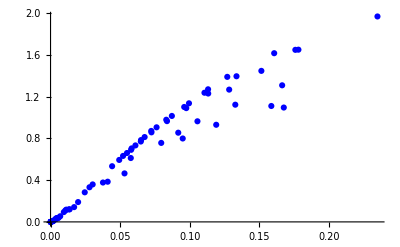

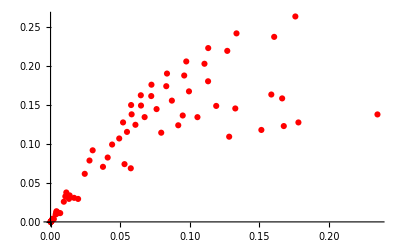

```mathematica
ListPlot[listV1V0,PlotStyle->Blue]
ListPlot[listS1S0,PlotStyle->Red]
```

```mathematica
(* -----------------------------------Lo que no quiere Miki *)
listV1V0={};listV2V0={};listV2V1={};listS1S0={};listS2S0={};listS2S1={};
Do[
{line,gchnum}=linelist[[1]][[i]];
(*{TnWO,αWO,βWO,V0WO,V1WO,V2WO}=getParams[resultsWO[[line]][[gchnum]][[5]]];*)
{TnW,αW,βW,V0W,V1W,V2W,S0W,S1W,S2W}=getParams[resultsW[[line]][[gchnum]][[5]]];

AppendTo[listV1V0,Table[{αW[[k]][[2]],Abs[V1W[[k]][[2]]/V0W[[k]][[2]]]},{k,1,Length[αW]}]];
AppendTo[listV2V0,Table[{αW[[k]][[2]],Abs[V2W[[k]][[2]]/V0W[[k]][[2]]]},{k,1,Length[αW]}]];
AppendTo[listV2V1,Table[{αW[[k]][[2]],Abs[V2W[[k]][[2]]/V1W[[k]][[2]]]},{k,1,Length[αW]}]];
AppendTo[listS1S0,Table[{αW[[k]][[2]],Abs[S1W[[k]][[2]]/S0W[[k]][[2]]]},{k,1,Length[αW]}]];
AppendTo[listS2S0,Table[{αW[[k]][[2]],Abs[S2W[[k]][[2]]/S0W[[k]][[2]]]},{k,1,Length[αW]}]];
AppendTo[listS2S1,Table[{αW[[k]][[2]],Abs[S2W[[k]][[2]]/S1W[[k]][[2]]]},{k,1,Length[αW]}]];,

{i,1,Length[linelist[[1]]]}]
```

```mathematica
GraphicsRow[{
Show[ListPlot[listV1V0,PlotStyle->Blue],ListPlot[listV2V0,PlotStyle->Orange]],
ListPlot[listV2V1,PlotStyle->Red]}]
```

```mathematica
GraphicsRow[{
Show[ListPlot[listS1S0,PlotStyle->Blue],ListPlot[listS2S0,PlotStyle->Orange]],
ListPlot[listS2S1,PlotStyle->Red]}]
```

```mathematica
(*--------------------------------------------Lo que quiere Miki ahora sí que sí*)
Get[NotebookDirectory[]<>"lodemiki.txt"];
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

```mathematica
(*{{gmax,m2,κ,λ,vev,Tn,α,{m23,kappa3,lambda3}},gmin,{lista de g versus beta}}*)
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 1 of {} does not exist.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

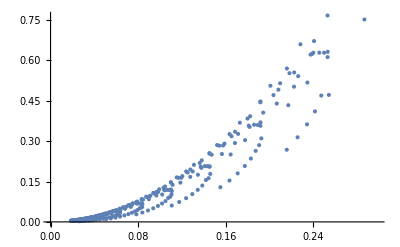

```mathematica
Clear[m2,λ,κ,g,T,α, ϵ];
V1V0values={};
δvevαvalues={};
Do[
{m2,κ,λ,T,g,α}={efts[[i]][[1]][[2]], efts[[i]][[1]][[3]], efts[[i]][[1]][[4]], efts[[i]][[1]][[6]], efts[[i]][[2]], efts[[i]][[1]][[7]] };
{V0val, V1val}=EffOpsPotValuesNew[];
If[α<0.3,
ratio=V1val[[2]]/V0val[[2]];
If[(α<0.25 &&ratio>0.01)||(α>0.25 &&ratio>0.1),
δvevα=VEVShiftNew[];
AppendTo[δvevαvalues,{α,δvevα}];
AppendTo[V1V0values,{α,ratio }];
];
];
Clear[m2,λ,κ,g,T, α,ϵ];
,{i, Length[efts]}]
ListPlot[δvevαvalues]
```

```mathematica
δvevαvalues
```

{{0.0241110589519983043,0.00629826},{0.0390402497539433999,0.016299},{0.0318284622550432036,0.0108941},{0.0259120983132829358,0.00774824},{0.0210627276000569554,0.0052823},{0.0631296707371238053,0.039966},{0.0515367537334742304,0.0281628},{0.0420166764494459277,0.0187347},{0.03420639085485256,0.0132505},{0.0278046119547389614,0.00898075},{0.0225636077607419099,0.00616288},{0.101958196004292581,0.101735},{0.0833367112205406074,0.069003},{0.0680326265411016207,0.0486227},{0.0554652758716353417,0.032395},{0.0451550898495736847,0.0228162},{0.0367047861802870037,0.0157827},{0.0297861615269391748,0.0105999},{0.0241277237638563985,0.00723538},{0.0195069497375180007,0.0048113},{0.164483214530691063,0.250443},{0.134594855309429995,0.175099},{0.110011962742272915,0.120498},{0.0898082635450522249,0.0841757},{0.0732193111418526638,0.0556901},{0.0596089126772612749,0.0395394},{0.0484534337613244659,0.0274341},{0.0393199486610452814,0.0182641},{0.0318511768848312171,0.0123499},{0.0257508121979879781,0.00823102},{0.0207759577798975331,0.00551288},{0.265070165075028286,7.72319},{0.21713123604188822,0.433518},{0.177675060969198578,0.303638},{0.14522552215943757,0.206631},{0.118555897468543114,0.145852},{0.0966565210150935605,0.0980702},{0.0786886639407760602,0.068487},{0.0639624165763035962,0.0466408},{0.0519064590506272128,0.0315445},{0.0420462496715441406,0.0214687},{0.0339936105450571388,0.0141912},{0.0274259366191246246,0.00944819},{0.022077460899395062,0.00630836},{0.286635284129020063,0.751816},{0.234546320856667184,0.517476},{0.191711086124373376,0.369885},{0.156503111492208497,0.252149},{0.127594443080101705,0.167188},{0.103875886092208131,0.118541},{0.0844368958413641707,0.0825075},{0.0685201729231056933,0.0545747},{0.0555052676596104605,0.0363553},{0.0448745479646214668,0.0245006},{0.0362043998810463383,0.0162811},{0.0291442858719621854,0.0101619},{0.0234042280519760441,0.00696986},{0.0187457209885035607,0.00462521},{0.25307562072239348,0.631736},{0.206599927978793813,0.439619},{0.168436841229304884,0.292907},{0.137126639493467761,0.20495},{0.111464621446566825,0.137976},{0.090452103020821531,0.0944499},{0.0732722561404763606,0.0638122},{0.0592378830351291477,0.0425347},{0.0477932418042690682,0.0280753},{0.038473068646979712,0.018313},{0.030895637476874023,0.0120041},{0.0247463928528582344,0.00779445},{0.0197655627243571545,0.00492677},{0.272729409194927053,0.817236},{0.222350758956853578,0.502321},{0.18101790531114062,0.357483},{0.147141068244128648,0.249701},{0.119406327313129571,0.163946},{0.0967252344247790108,0.111047},{0.0782004405314173368,0.0733426},{0.0630923556858743878,0.0487031},{0.0507878202209456967,0.0301868},{0.0407846394676781229,0.0207456},{0.0326671142614488388,0.0137806},{0.0260922592465696983,0.00842518},{0.020778731592756363,0.00545807},{0.293523124428293702,0.893451},{0.238959044551718847,0.624044},{0.194240674894684551,0.405856},{0.157627503240501621,0.283975},{0.12768511168078156,0.194606},{0.103231672063008692,0.127241},{0.0832864693762138397,0.0837989},{0.0670440387019751727,0.0540785},{0.053839632705110739,0.0358725},{0.0431237400476996782,0.0235656},{0.0344442032446567251,0.014508},{0.0274296361305804044,0.00943258},{0.0217739518670472532,0.00591394},{0.256414488418303277,30.8354},{0.208082467950693323,0.49118},{0.168556084442867488,0.33492},{0.136275316244539257,0.21878},{0.109946236246399903,0.146477},{0.0885043870079865042,0.0921383},{0.0710733419646514403,0.0621493},{0.0569265194138622241,0.0406356},{0.0454693430683635463,0.0254535},{0.0362099579540960254,0.0162505},{0.0287436746993058462,0.0105261},{0.0227391265568066998,0.00629954},{0.274685725695244964,0.850237},{0.222509657623926993,0.555158},{0.179894798154348917,0.384032},{0.14513848903997531,0.253484},{0.116833940115142212,0.163807},{0.0938235265639011384,0.107842},{0.075147869596591893,0.0691708},{0.0600236994671648066,0.0437192},{0.0477996738306298991,0.0281945},{0.0379440678604672094,0.018302},{0.0300179194941122621,0.0108163},{0.0236606345600200788,0.00670928},{0.0185776365546463165,0.00409792},{0.293730058507007563,0.929771},{0.237474523639465224,0.621409},{0.191596579523193339,0.447365},{0.154230861676599301,0.283043},{0.123856147940773362,0.187333},{0.0992037752854160737,0.121082},{0.0792371860122555449,0.0756172},{0.0630999157352148121,0.0487508},{0.0500900812083240402,0.0313},{0.0396259737078416066,0.0184024},{0.0312341266861364576,0.0116197},{0.0245240448834397294,0.00709128},{0.0191763087100244624,0.00423755},{0.252921029397245145,0.788952},{0.203599260502490026,0.471032},{0.163498724521108724,0.326259},{0.13095658785691594,0.211933},{0.104600412229710588,0.13152},{0.0832981798435135507,0.0846076},{0.0661230731968201757,0.0539287},{0.0523106153577005545,0.0324591},{0.0412319372158622827,0.0201024},{0.0323740116582434886,0.0122449},{0.0197076718481732846,0.00432064},{0.215832719075660012,0.569868},{0.172874008484286579,0.368455},{0.138080727500272893,0.228621},{0.109960582480303659,0.146999},{0.087288112452549721,0.0935168},{0.0690543435731968691,0.0562811},{0.0544298660501781675,0.0348656},{0.0427364797750677886,0.0212409},{0.0260158543950598231,0.00754229},{0.0201603018021935844,0.00435515},{0.284919045567395224,1.0236},{0.228208886984014675,0.659626},{0.182279010937532876,0.392356},{0.145158090586697791,0.255538},{0.115229266459250523,0.165345},{0.0911568314278643072,0.0975775},{0.0718518576085483279,0.0609271},{0.056416102626728637,0.0368294},{0.0441141251621454053,0.0221344},{0.0343433844067003447,0.0128747},{0.0266135072582891104,0.00753053},{0.0205224993838739461,0.00433384},{0.240623875141631166,0.671756},{0.191622597236539433,0.444279},{0.152110249294061556,0.285382},{0.120334715672251999,0.170051},{0.094850408853388371,0.105147},{0.0744742848588686168,0.0639073},{0.0453363684497989986,0.0224362},{0.0351320548187340348,0.0130431},{0.0270915773317313632,0.00750576},{0.0207837513217048915,0.00423813},{0.252960003860380867,0.766642},{0.200802107804982255,0.505721},{0.158856270233550589,0.290756},{0.125211898875757732,0.183451},{0.0983124243592987529,0.111187},{0.0598479461400858934,0.0399368},{0.0463774681048324602,0.0226382},{0.0357634275606652161,0.0129996},{0.0274365280929921747,0.00735127},{0.0209348328719295325,0.0041677},{0.265072619668900833,0.861936},{0.209703522080208177,0.514946},{0.165292861889197534,0.318157},{0.129782671748359224,0.187521},{0.0790045454735525954,0.0687934},{0.061223024113589139,0.0393276},{0.0472106615409383715,0.0225666},{0.0362187051748168107,0.012748},{0.0276358817118818531,0.00724106},{0.0209676664388137694,0.00390532},{0.218201670754726657,0.552375},{0.171324262586163234,0.326914},{0.10429375091765565,0.117612},{0.0808190519940582275,0.0683855},{0.0623225042284571706,0.0392035},{0.0478118248690284214,0.022244},{0.0364820469810380466,0.0125237},{0.0276791588636604059,0.006548},{0.0208762856248139415,0.00397445},{0.288049058428451021,0.980394},{0.226164890092717785,0.541224},{0.137678172610294275,0.200704},{0.106689783795492668,0.119},{0.0822710896272759867,0.0682039},{0.0631161637364824613,0.0383503},{0.0481595754260639442,0.0218245},{0.0365392828221537541,0.0118516},{0.0275587546782944046,0.00623526},{0.0206576409137380415,0.00338962},{0.298555115877918831,0.955821},{0.18174664068814958,0.35281},{0.140839614237868782,0.207167},{0.108605336029233945,0.118715},{0.0833190051837121026,0.0670013},{0.0635749394574905563,0.0378528},{0.0363799755037187075,0.0122721},{0.0272702062159956259,0.00598238},{0.239922307196860335,0.628394},{0.18592139231309987,0.360817},{0.143369264029688803,0.206954},{0.109990156868322961,0.116925},{0.083925319621093869,0.066061},{0.0480256617234021965,0.0194473},{0.0359987905309903378,0.0101966},{0.0268114476232964201,0.00545261},{0.245429245631583443,0.628706},{0.189262144060312942,0.360044},{0.145194726912528299,0.204676},{0.110788324192814147,0.114734},{0.0633973062898215145,0.0335882},{0.0475216264833229624,0.0175418},{0.0353932427727960894,0.00935309},{0.0261857922734012698,0.00483706},{0.249843012997101183,0.628248},{0.191670707222724557,0.356993},{0.0836910019365759567,0.0551799},{0.0627327800494135862,0.0307575},{0.0467223178014449098,0.0168162},{0.034567726151462079,0.00840865},{0.0253998373345389883,0.00426324},{0.253025559482228435,0.611948},{0.110478762331573013,0.101904},{0.0828127979686258259,0.0536072},{0.0616782285981627293,0.0283011},{0.0456323070326242058,0.0146328},{0.0335301362114288556,0.00741336},{0.0244637900139397721,0.00369456},{0.145842506424928381,0.178301},{0.109321046671975897,0.0934994},{0.0814215300999630159,0.0507225},{0.060239045678474594,0.0254845},{0.0442628844916723024,0.0129044},{0.0322943718693123535,0.00642622},{0.0233917469398285116,0.00314731},{0.192524629053733409,0.310287},{0.144313466097825749,0.162266},{0.107482599354847594,0.0889848},{0.0795210856969903873,0.044406},{0.0584308878691942243,0.0224781},{0.0426313582826367346,0.0111881},{0.0308791513901019686,0.00547547},{0.254151055409081172,0.471618},{0.190507597590631878,0.285018},{0.141887817619325118,0.155568},{0.104974984252200851,0.0774054},{0.077134192559689771,0.0391756},{0.0562778129684122982,0.0194932},{0.0407632514175756827,0.00953506},{0.0293075341627093838,0.00458533},{0.251487933946307862,16.9945},{0.187303802464318214,0.263794},{0.138576241941353789,0.134957},{0.101823639989718537,0.0683},{0.0742913222969550369,0.0339796},{0.0538113188452184893,0.0166165},{0.0386886444638169721,0.00798634},{0.0276061770493613405,0.00377317},{0.247256486046914442,0.469323},{0.182934717122330198,0.235334},{0.134416619761175554,0.119097},{0.0980714304136578591,0.0592487},{0.0710360838198210026,0.0289696},{0.0510726948067294836,0.0139199},{0.0364421662300990212,0.00657295},{0.025803479939016067,0.00305057},{0.24149014566498142,0.410383},{0.177443677263681016,0.207706},{0.129462406923587015,0.10333},{0.0937735823927710877,0.0505197},{0.0674202067115457771,0.0242718},{0.0481073290299424902,0.0114581},{0.0340628538417775129,0.00531498},{0.234238956774356244,0.362226},{0.170902677284685028,0.180224},{0.123789358006342429,0.0881175},{0.0890017740806191976,0.0423356},{0.063505517597500491,0.0199823},{0.0449666686694956408,0.00926663},{0.031591206348218992,0.00422243},{0.225605535698315485,0.314339},{0.163414061856046483,0.153712},{0.117489048977227617,0.073849},{0.0838331042116335634,0.0348567},{0.0593593455123090849,0.0161628},{0.0417036573147463868,0.0073627},{0.0290689712055607931,0.00329564},{0.215720335534947183,0.268124},{0.155096097203750116,0.128832},{0.110667967527303249,0.0608149},{0.0783606148380926043,0.0281985},{0.0550526725664867919,0.0128437},{0.0383734116922972435,0.00574712},{0.0265366849297769582,0.00252724},{0.0506567970020482539,0.0100268},{0.0350306156500051966,0.00440768}}

```mathematica
V1V0values
```

{{0.0241110589519983043,0.0141447},{0.0390402497539433999,0.0382379},{0.0318284622550432036,0.0252225},{0.0259120983132829358,0.0177008},{0.0210627276000569554,0.0118849},{0.0631296707371238053,0.0973036},{0.0515367537334742304,0.0679406},{0.0420166764494459277,0.0446667},{0.03420639085485256,0.0312166},{0.0278046119547389614,0.0208618},{0.0225636077607419099,0.0141014},{0.101958196004292581,0.25553},{0.0833367112205406074,0.172143},{0.0680326265411016207,0.120424},{0.0554652758716353417,0.0794324},{0.0451550898495736847,0.0553754},{0.0367047861802870037,0.0378429},{0.0297861615269391748,0.0250588},{0.0241277237638563985,0.0168471},{0.0195069497375180007,0.0110157},{0.164483214530691063,0.643791},{0.134594855309429995,0.448876},{0.110011962742272915,0.307523},{0.0898082635450522249,0.213656},{0.0732193111418526638,0.14018},{0.0596089126772612749,0.0987286},{0.0484534337613244659,0.0678052},{0.0393199486610452814,0.0445707},{0.0318511768848312171,0.0297231},{0.0257508121979879781,0.0195037},{0.0207759577798975331,0.0128451},{0.265070165075028286,23.9454},{0.21713123604188822,1.13316},{0.177675060969198578,0.793016},{0.14522552215943757,0.538105},{0.118555897468543114,0.378651},{0.0966565210150935605,0.253096},{0.0786886639407760602,0.175627},{0.0639624165763035962,0.118574},{0.0519064590506272128,0.0793617},{0.0420462496715441406,0.0533712},{0.0339936105450571388,0.0347817},{0.0274259366191246246,0.0227992},{0.022077460899395062,0.0149662},{0.286635284129020063,1.99448},{0.234546320856667184,1.37334},{0.191711086124373376,0.982207},{0.156503111492208497,0.668107},{0.127594443080101705,0.441067},{0.103875886092208131,0.311567},{0.0844368958413641707,0.215587},{0.0685201729231056933,0.141321},{0.0555052676596104605,0.0931631},{0.0448745479646214668,0.0620439},{0.0362043998810463383,0.0406594},{0.0291442858719621854,0.0249541},{0.0234042280519760441,0.0168356},{0.0187457209885035607,0.0109659},{0.25307562072239348,1.70453},{0.206599927978793813,1.18669},{0.168436841229304884,0.788887},{0.137126639493467761,0.550925},{0.111464621446566825,0.369156},{0.090452103020821531,0.25125},{0.0732722561404763606,0.168417},{0.0592378830351291477,0.111137},{0.0477932418042690682,0.0724732},{0.038473068646979712,0.046607},{0.030895637476874023,0.0300712},{0.0247463928528582344,0.0191833},{0.0197655627243571545,0.0118888},{0.272729409194927053,2.24823},{0.222350758956853578,1.37725},{0.18101790531114062,0.980944},{0.147141068244128648,0.684338},{0.119406327313129571,0.447104},{0.0967252344247790108,0.301183},{0.0782004405314173368,0.197322},{0.0630923556858743878,0.129762},{0.0507878202209456967,0.0793499},{0.0407846394676781229,0.0538479},{0.0326671142614488388,0.0352192},{0.0260922592465696983,0.0211248},{0.020778731592756363,0.0134206},{0.293523124428293702,2.4919},{0.238959044551718847,1.74433},{0.194240674894684551,1.13249},{0.157627503240501621,0.79211},{0.12768511168078156,0.54136},{0.103231672063008692,0.351812},{0.0832864693762138397,0.229939},{0.0670440387019751727,0.146888},{0.053839632705110739,0.0963413},{0.0431237400476996782,0.0624301},{0.0344442032446567251,0.0377752},{0.0274296361305804044,0.0241248},{0.0217739518670472532,0.0148186},{0.256414488418303277,183.},{0.208082467950693323,1.39806},{0.168556084442867488,0.952785},{0.136275316244539257,0.620047},{0.109946236246399903,0.413238},{0.0885043870079865042,0.257702},{0.0710733419646514403,0.172397},{0.0569265194138622241,0.111438},{0.0454693430683635463,0.0687754},{0.0362099579540960254,0.0431956},{0.0287436746993058462,0.0274759},{0.0227391265568066998,0.016088},{0.274685725695244964,2.46398},{0.222509657623926993,1.60874},{0.179894798154348917,1.11386},{0.14513848903997531,0.733279},{0.116833940115142212,0.471387},{0.0938235265639011384,0.308334},{0.075147869596591893,0.195896},{0.0600236994671648066,0.122319},{0.0477996738306298991,0.0778036},{0.0379440678604672094,0.0497046},{0.0300179194941122621,0.0287762},{0.0236606345600200788,0.0174714},{0.0185776365546463165,0.0104215},{0.293730058507007563,2.7389},{0.237474523639465224,1.83383},{0.191596579523193339,1.32487},{0.154230861676599301,0.835184},{0.123856147940773362,0.55079},{0.0992037752854160737,0.353667},{0.0792371860122555449,0.218668},{0.0630999157352148121,0.13941},{0.0500900812083240402,0.0882812},{0.0396259737078416066,0.0509391},{0.0312341266861364576,0.0315563},{0.0245240448834397294,0.0188347},{0.0191763087100244624,0.0109801},{0.252921029397245145,2.38639},{0.203599260502490026,1.41925},{0.163498724521108724,0.984115},{0.13095658785691594,0.636934},{0.104600412229710588,0.392269},{0.0832981798435135507,0.250229},{0.0661230731968201757,0.157707},{0.0523106153577005545,0.0934408},{0.0412319372158622827,0.0568761},{0.0323740116582434886,0.0339478},{0.0197076718481732846,0.0114072},{0.215832719075660012,1.75929},{0.172874008484286579,1.13618},{0.138080727500272893,0.701522},{0.109960582480303659,0.448579},{0.087288112452549721,0.282982},{0.0690543435731968691,0.168096},{0.0544298660501781675,0.102621},{0.0427364797750677886,0.0614083},{0.0260158543950598231,0.0208439},{0.0201603018021935844,0.0117163},{0.284919045567395224,3.23085},{0.228208886984014675,2.08466},{0.182279010937532876,1.23465},{0.145158090586697791,0.802536},{0.115229266459250523,0.516876},{0.0911568314278643072,0.301677},{0.0718518576085483279,0.186236},{0.056416102626728637,0.110852},{0.0441141251621454053,0.0653997},{0.0343433844067003447,0.0372003},{0.0266135072582891104,0.0212242},{0.0205224993838739461,0.0118795},{0.240623875141631166,2.16162},{0.191622597236539433,1.43215},{0.152110249294061556,0.918237},{0.120334715672251999,0.542941},{0.094850408853388371,0.332838},{0.0744742848588686168,0.199848},{0.0453363684497989986,0.0677308},{0.0351320548187340348,0.0384876},{0.0270915773317313632,0.0215796},{0.0207837513217048915,0.0118346},{0.252960003860380867,2.52875},{0.200802107804982255,1.67241},{0.158856270233550589,0.955216},{0.125211898875757732,0.600048},{0.0983124243592987529,0.360399},{0.0598479461400858934,0.125841},{0.0463774681048324602,0.0698528},{0.0357634275606652161,0.0391727},{0.0274365280929921747,0.0215566},{0.0209348328719295325,0.0118582},{0.265072619668900833,2.91564},{0.209703522080208177,1.73882},{0.165292861889197534,1.072},{0.129782671748359224,0.627395},{0.0790045454735525954,0.225501},{0.061223024113589139,0.126664},{0.0472106615409383715,0.0711817},{0.0362187051748168107,0.0392256},{0.0276358817118818531,0.0216639},{0.0209676664388137694,0.0113108},{0.218201670754726657,1.91177},{0.171324262586163234,1.12735},{0.10429375091765565,0.399837},{0.0808190519940582275,0.229375},{0.0623225042284571706,0.129199},{0.0478118248690284214,0.0717347},{0.0364820469810380466,0.0393634},{0.0276791588636604059,0.0199476},{0.0208762856248139415,0.0117372},{0.288049058428451021,3.47986},{0.226164890092717785,1.91262},{0.137678172610294275,0.705435},{0.106689783795492668,0.41457},{0.0822710896272759867,0.234294},{0.0631161637364824613,0.129313},{0.0481595754260639442,0.071979},{0.0365392828221537541,0.0380192},{0.0275587546782944046,0.0193669},{0.0206576409137380415,0.0101666},{0.298555115877918831,3.46312},{0.18174664068814958,1.28001},{0.140839614237868782,0.747413},{0.108605336029233945,0.423918},{0.0833190051837121026,0.235754},{0.0635749394574905563,0.130713},{0.0363799755037187075,0.0402974},{0.0272702062159956259,0.0189482},{0.239922307196860335,2.34807},{0.18592139231309987,1.34392},{0.143369264029688803,0.765932},{0.109990156868322961,0.428099},{0.083925319621093869,0.238309},{0.0480256617234021965,0.0669804},{0.0359987905309903378,0.0340478},{0.0268114476232964201,0.0175857},{0.245429245631583443,2.41001},{0.189262144060312942,1.3765},{0.145194726912528299,0.77748},{0.110788324192814147,0.431026},{0.0633973062898215145,0.121397},{0.0475216264833229624,0.0616698},{0.0353932427727960894,0.0318541},{0.0261857922734012698,0.0158703},{0.249843012997101183,2.47357},{0.191670707222724557,1.40209},{0.0836910019365759567,0.20826},{0.0627327800494135862,0.113677},{0.0467223178014449098,0.060481},{0.034567726151462079,0.0291878},{0.0253998373345389883,0.0142218},{0.253025559482228435,2.4741},{0.110478762331573013,0.402482},{0.0828127979686258259,0.207698},{0.0616782285981627293,0.107018},{0.0456323070326242058,0.0536621},{0.0335301362114288556,0.0262057},{0.0244637900139397721,0.012519},{0.145842506424928381,0.732779},{0.109321046671975897,0.378599},{0.0814215300999630159,0.201618},{0.060239045678474594,0.0985334},{0.0442628844916723024,0.0482725},{0.0322943718693123535,0.0231128},{0.0233917469398285116,0.0108208},{0.192524629053733409,1.32189},{0.144313466097825749,0.684168},{0.107482599354847594,0.370357},{0.0795210856969903873,0.180532},{0.0584308878691942243,0.0888005},{0.0426313582826367346,0.0426568},{0.0308791513901019686,0.0200162},{0.254151055409081172,2.05773},{0.190507597590631878,1.2477},{0.141887817619325118,0.675519},{0.104974984252200851,0.329849},{0.077134192559689771,0.163006},{0.0562778129684122982,0.0786293},{0.0407632514175756827,0.0370177},{0.0293075341627093838,0.0170162},{0.251487933946307862,194.107},{0.187303802464318214,1.1885},{0.138576241941353789,0.600681},{0.101823639989718537,0.298369},{0.0742913222969550369,0.14462},{0.0538113188452184893,0.0683771},{0.0386886444638169721,0.0315348},{0.0276061770493613405,0.0141947},{0.247256486046914442,2.19207},{0.182934717122330198,1.08996},{0.134416619761175554,0.544291},{0.0980714304136578591,0.265224},{0.0710360838198210026,0.126026},{0.0510726948067294836,0.0583753},{0.0364421662300990212,0.0263623},{0.025803479939016067,0.0116156},{0.24149014566498142,1.97031},{0.177443677263681016,0.989282},{0.129462406923587015,0.484745},{0.0937735823927710877,0.231599},{0.0674202067115457771,0.107828},{0.0481073290299424902,0.0489093},{0.0340628538417775129,0.0216193},{0.234238956774356244,1.79096},{0.170902677284685028,0.882604},{0.123789358006342429,0.424145},{0.0890017740806191976,0.198606},{0.063505517597500491,0.0905531},{0.0449666686694956408,0.0402034},{0.031591206348218992,0.0173888},{0.225605535698315485,1.60057},{0.163414061856046483,0.773789},{0.117489048977227617,0.364502},{0.0838331042116335634,0.167173},{0.0593593455123090849,0.0746158},{0.0417036573147463868,0.0324131},{0.0290689712055607931,0.0137143},{0.215720335534947183,1.40583},{0.155096097203750116,0.666368},{0.110667967527303249,0.307557},{0.0783606148380926043,0.138099},{0.0550526725664867919,0.06031},{0.0383734116922972435,0.0256246},{0.0265366849297769582,0.010604},{0.0506567970020482539,0.0478042},{0.0350306156500051966,0.0198619}}